```mathematica
Clear["Global`*"]
```

{{0.,1},{0.1,1.21034},{0.2,1.41068},{0.3,1.59889},{0.4,1.773},{0.5,1.9311},{0.6,2.07145},{0.7,2.19248},{0.8,2.29277},{0.9,2.37113},{1.,2.42653}}

{{x[t]→Cos[t]+2 Sin[t]}}

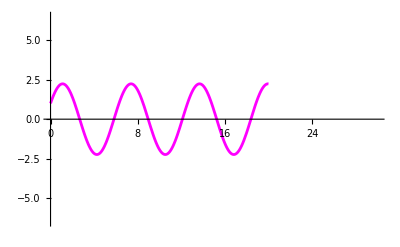

```mathematica
f[x_,t_]:=-x;
f1[x1_,x2_,t_]:= x2;
f2[x1_,x2_,t_]:= -x1;

(*Error message*)
RK::nonnegativeint = "Nmax must be a non-negative integer";

RK[dt_,Nmax_,a1_,a2_]:= Module[{j = 0,n,g1,g2,g3,g4,h1,h2,h3,h4,x1,x2,t},If[Or[Nmax≤ 0,Not[IntegerQ[Nmax]]],Message[RK::nonnegativeint],
x1[0]:=a1;x2[0]:= a2;
g1[j_]:=(g1[j] =f1[x1[j],x2[j],t]);
g2[j_]:=(g2[j] =f1[x1[j]+dt/2  g1[j],x2[j]+dt/2  g1[j],t+dt/2]);
g3[j_]:=(g3[j] =f1[x1[j]+dt/2  g2[j],x2[j] +dt/2 g2[j],t +dt/2]);
g4[j_]:=(g4[j] =f1[x1[j]+dt g3[j] ,x2[j] +dt g3[j],t+dt]);
x1[j_] := (x1[j] =x1[j-1]+ dt/6(g1[j-1] +2g2[j-1]+2g3[j-1]+g4[j-1]));
h1[j_]:=(h1[j]=f2[x1[j],x2[j],t]);
h2[j_]:=(h2[j]=f2[x1[j]+dt /2  h1[j],x2[j]+dt/2  h1[j],t+dt/2]);
h3[j_]:=(h3[j]=f2[x1[j]+dt /2  h2[j],x2[j]+dt/2  h2[j],t +dt/2]);
h4[j_]:=(h4[j]=f2[x1[j]+dt h3[j] ,x2[j] +dt h3[j],t+dt]);
x2[j_] := (x2[j] = x2[j-1]+dt/6(h1[j-1] + 2h2[j-1]+2h3[j-1]+h4[j-1]));
Table[{j dt,x1[j]},{j,0,Nmax}]
]
];
RK[.1,10,1,2]
asol[a1_,a2_] := DSolve[{x''[t] == f[x[t],t],x[0] == a1,x'[0] == a2},x[t],t];

asol[1,2]

agraph[a1_,a2_,tlast_]:= Plot[Evaluate[x[t]/.asol[a1,a2]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,0,1]},PlotRange->{{0,30},{-6.5,6.5}}];

RKgraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[RK[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,1,0]},PlotRange->{{0,30},{-6.5,6.5}}];

Show[RKgraph[.004,1000,1,2],agraph[1,2,20]]
```

```mathematica
RK[.1,10,1,2]
```

RK[0.1,10,1,2]

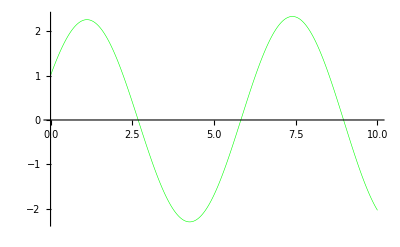

```mathematica
RKgraph[dt_,Nmax_,a1_,a2_]:= ListLinePlot[RK[dt,Nmax,a1,a2],PlotStyle->{Thickness[0.001],RGBColor[0,1,0]},PlotRange->All];
RKgraph[.01,1000,1,2]
```

{{x[t]→Cos[t]+2 Sin[t]}}

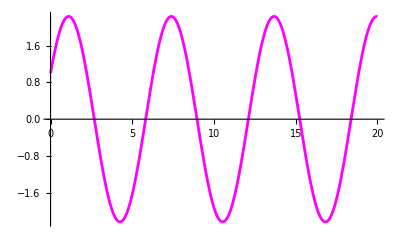

```mathematica
asol[a1_,a2_] := DSolve[{x''[t] == f[x[t],t],x[0] == a1,x'[0] == a2},x[t],t];

asol[1,2]

agraph[a1_,a2_,tlast_]:= Plot[Evaluate[x[t]/.asol[a1,a2]],{t,0,tlast},PlotStyle->{Thickness[0.005],RGBColor[1,0,1]},PlotRange->All];agraph[1,2,20]
```

```mathematica
Show[RKgraph[.01,1000,1,2],agraph[1,2,20]]
```

```mathematica
runge[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,k1,k2,k3,k4,m1,m2,m3,m4,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
k1[j_]:=(k1[j]= f1[x1[j],x2[j],t]);
k2[j_]:=(k2[j]= f1[x1[j]+dt/2 k1[j],x2[j]+dt/2 k1[j],t+dt/2]);
k3[j_]:=(k3[j]=f1[x1[j]+dt/2 k2[j],x2[j]+dt/2 k2[j],t+dt/2]);
k4[j_]:=(k4[j]=f1[x1[j]+dt k3[j],x2[j]+dt k3[j],t+dt]);
m1[j_]:=(m1[j]=f2[x1[j],x2[j],t]);
m2[j_]:=(m2[j]=f2[x1[j]+dt/2 m1[j],x2[j]+dt/2 m1[j],t+dt/2]);
m3[j_]:=(m3[j]=f2[x1[j]+dt/2 m2[j],x2[j]+dt/2 m2[j],t+dt/2]);
m4[j_]:=(m4[j]=f2[x1[j]+dt m3[j],x2[j]+dt m3[j],t+dt]);
x1[j_]:=(x1[j]=x1[j-1]+dt/6(k1[j-1]+2 k2[j-1]+2 k3[j-1]+k4[j-1]));
x2[j_]:=(x2[j]=x2[j-1]+dt/6(m1[j-1]+2 m2[j-1]+2 m3[j-1]+m4[j-1]));
Table[{j dt,x1[j]},{j,0,Nmax}]
]
];
```

```mathematica
rungegraph[dt_, Nmax_, a1_, a2_] := ListLinePlot[runge[dt, Nmax, a1, a2], PlotRange -> All, PlotStyle -> RGBColor[0, 0, 0]]
```

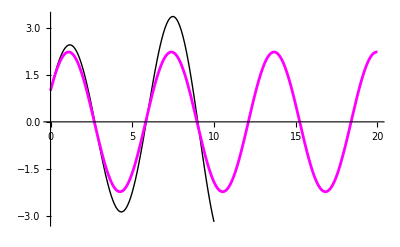

```mathematica
Show[rungegraph[.1,100,1,2],agraph[1,2,20]]
```